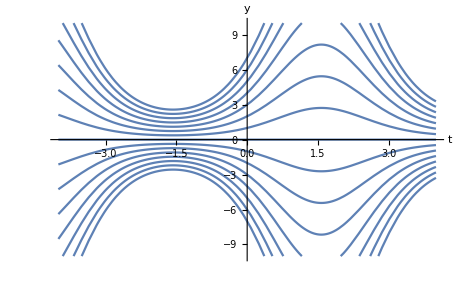
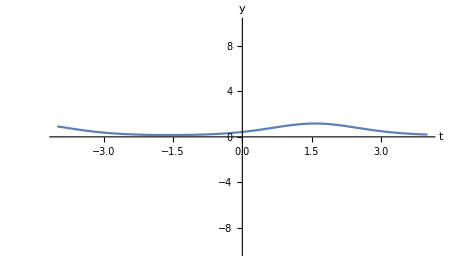
Equazione iniziale: y'=y cos(t)

solution=DSolve[y'[t]==y[t]*Cos[t],y[t],t]

{{y[t]→ⅇ^Sin[t] C[1]}}

f[t_]=y[t]/.solution[[1]]
F[t_]=Table[f[t]/.C[1]->j,{j,-7,7}]
Plot[F[t],{t,-4,4},AxesLabel->{t,y},PlotRange->{-10,10}]

-Graphics-


Condizione data: y(1)=-1

cauchy=DSolve[{y'[t]==y[t]*Cos[t],y[1]==1},y[t],t]

{{y[t]→ⅇ^(-Sin[1]+Sin[t])}}

g[t_]=y[t]/.cauchy[[1]]
Plot[g[t],{t,-4,4},AxesLabel->{t,y},PlotRange->{-10,10}]

-Graphics-